```mathematica
ClearAll;
Density=1000.0;
Gravity=9.8;
Zin=0.5;
As=0.04*0.04;
At=1.0;
K=As*Density*Sqrt[2*Gravity]/At;
```

```mathematica
Eq1 = Z'[t] == -K*Sqrt[Z[t]];
Eq1 = Z'[t] == -K*Z[t];
```

```mathematica
ZZ[t_]=Z[t]/.First@FullSimplify[DSolve[{Eq1,Z[0]==Zin},Z[t],t]]
```

0.5 ⅇ^(-7.0835 t)

```mathematica
ZZ[t]
```

0.5 ⅇ^(-7.0835 t)

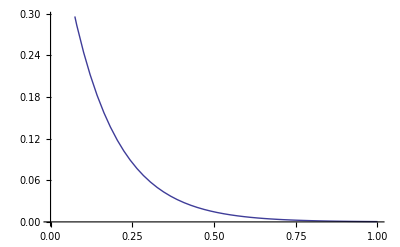

```mathematica
Plot[ZZ[t],{t,0,1}]
```